```mathematica
ClearAll["Global`*"];
(*[amin,amax] are the x-corners of the element in the topological space [-1,1] *)
(*[bmin,bmax] are the x-corners of the element in the topological space [1,2] *)
```

```mathematica
a[r_]:=amin + (amax-amin)*(r+1)/2;
b[s_]:=bmin + (bmax-bmin)*(s+1)/2;
```

```mathematica
m=(2-1)/((1/R2)-(1/R1));
n=(1*R1-2*R2)/(R1-R2);
R[s_]=m/(b[s]-n);
```

```mathematica
x[r_]:=Tan [a[r]*π/4];
q[r_,s_]:=R[s]/Sqrt [x[r]^2+1];
xf[r_,s_]:=+q[r,s]*x[r];
yf[r_,s_]:=+q[r,s];
```

```mathematica
xr = D[xf[r,s],r]; xs = D[xf[r,s],s]; 
yr = D[yf[r,s],r]; ys = D[yf[r,s],s];
```

```mathematica
dxdr = {{xr,xs},{yr,ys}};
J = xr*(ys)-yr*(xs);
drdx={{ys/J,-xs/J},{-yr/J,xr/J}};
drdxJ={{(ys),-(xs)},{-(yr),(xr)}};
```

```mathematica
Do[Print[StringReplace[StringJoin["dxyz_drst[",ToString[i-1],"][",ToString[j-1],"] = ",ToString[CForm[Simplify[dxdr[[i]][[j]]]]],";"],{"Power"->"pow", "Pi"->"M_PI","Sin"->"sin","Cos"->"cos","Tan"->"tan","Sqrt"->"sqrt","Sec"->"secant_fcn"}]],{i,2},{j,2}]
StringReplace[StringJoin["jacobian = ",ToString[CForm[Simplify[J]] ] , ";"],{"Power"->"pow", "Pi"->"M_PI","Sin"->"sin","Cos"->"cos","Tan"->"tan","Sqrt"->"sqrt","Sec"->"secant_fcn"}]
Do[Print[StringReplace[StringJoin["drst_dxyz[",ToString[i-1],"][",ToString[j-1],"] = ",ToString[CForm[Simplify[drdx[[i]][[j]]]]],";"],{"Power"->"pow", "Pi"->"M_PI","Sin"->"sin","Cos"->"cos","Tan"->"tan","Sqrt"->"sqrt","Sec"->"secant_fcn"}]],{i,2},{j,2}]
Do[Print[StringReplace[StringJoin["drst_dxyz[",ToString[i-1],"][",ToString[j-1],"] = ",ToString[CForm[Simplify[drdx[[i]][[j]]]]],";"],{"Power"->"pow", "Pi"->"M_PI","Sin"->"sin","Cos"->"cos","Tan"->"tan","Sqrt"->"sqrt","Sec"->"secant_fcn"}]],{i,2},{j,2}]
Do[Print[StringReplace[StringJoin["sj_sqr_vol[",ToString[i-1],"] = ",ToString[CForm[Simplify[Sum[drdxJ[[i]][[k]]*drdxJ[[i]][[k]],{k,1,2}]]]],";"],{"Power"->"pow", "Pi"->"M_PI","Sin"->"sin","Cos"->"cos","Tan"->"tan","Sqrt"->"sqrt","Sec"->"secant_fcn"}]],{i,2}]
Do[Print[StringReplace[StringJoin["sj_sqr_div_J_sqr_vol[",ToString[i-1],"] = ",ToString[CForm[Simplify[Sum[drdx[[i]][[k]]*drdx[[i]][[k]],{k,1,2}]]]],";"],{"Power"->"pow", "Pi"->"M_PI","Sin"->"sin","Cos"->"cos","Tan"->"tan","Sqrt"->"sqrt","Sec"->"secant_fcn"}]],{i,2}]
Do[Print[StringReplace[StringJoin["sj_sqr_div_J_vol[",ToString[i-1],"] = ",ToString[CForm[Simplify[Sum[drdxJ[[i]][[k]]*drdx[[i]][[k]],{k,1,2}]]]],";"],{"Power"->"pow", "Pi"->"M_PI","Sin"->"sin","Cos"->"cos","Tan"->"tan","Sqrt"->"sqrt","Sec"->"secant_fcn"}]],{i,2}]
Do[Print[StringReplace[StringJoin["drst_dxyz_times_jac[",ToString[i-1],"][",ToString[j-1],"] = ",ToString[CForm[Simplify[drdxJ[[i]][[j]]]]],";"],{"Power"->"pow", "Pi"->"M_PI","Sin"->"sin","Cos"->"cos","Tan"->"tan","Sqrt"->"sqrt","Sec"->"secant_fcn"}]],{i,2},{j,2}]
Do[Print[StringReplace[StringJoin["drdxJdrdx[",ToString[i-1],"][",ToString[j-1],"] = ",ToString[CForm[Simplify[Sum[drdxJ[[i]][[k]]*drdx[[j]][[k]],{k,1,2}]]]],";"],{"Power"->"pow", "Pi"->"M_PI","Sin"->"sin","Cos"->"cos","Tan"->"tan","Sqrt"->"sqrt","Sec"->"secant_fcn"}]],{i,2},{j,2}]
```

dxyz_drst[0][0] = ((amax - amin)*M_PI*R1*R2)/(4.*(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s))*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

dxyz_drst[0][1] = (-2*(bmax - bmin)*R1*(R1 - R2)*R2*tan((M_PI*(amax + amin + amax*r - amin*r))/8.))/(pow(R2*(-4 + bmax + bmin + bmax*s - bmin*s) - R1*(-2 + bmax + bmin + bmax*s - bmin*s),2)*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

dxyz_drst[1][0] = -((amax - amin)*M_PI*R1*R2*tan((M_PI*(amax + amin + amax*r - amin*r))/8.))/(4.*(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s))*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

dxyz_drst[1][1] = (-2*(bmax - bmin)*R1*(R1 - R2)*R2)/(pow(R2*(-4 + bmax + bmin + bmax*s - bmin*s) - R1*(-2 + bmax + bmin + bmax*s - bmin*s),2)*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

jacobian = -((amax - amin)*(bmax - bmin)*M_PI*pow(R1,2)*(R1 - R2)*pow(R2,2))/(2.*pow(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s),3));

drst_dxyz[0][0] = (4*(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s)))/((amax - amin)*M_PI*R1*R2*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

drst_dxyz[0][1] = (-2*(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s))*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2))*sin((M_PI*(amax + amin + amax*r - amin*r))/4.))/((amax - amin)*M_PI*R1*R2);

drst_dxyz[1][0] = -(pow(R2*(-4 + bmax + bmin + bmax*s - bmin*s) - R1*(-2 + bmax + bmin + bmax*s - bmin*s),2)*tan((M_PI*(amax + amin + amax*r - amin*r))/8.))/(2.*(bmax - bmin)*R1*(R1 - R2)*R2*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

drst_dxyz[1][1] = -pow(R2*(-4 + bmax + bmin + bmax*s - bmin*s) - R1*(-2 + bmax + bmin + bmax*s - bmin*s),2)/(2.*(bmax - bmin)*R1*(R1 - R2)*R2*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

drst_dxyz[0][0] = (4*(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s)))/((amax - amin)*M_PI*R1*R2*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

drst_dxyz[0][1] = (-2*(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s))*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2))*sin((M_PI*(amax + amin + amax*r - amin*r))/4.))/((amax - amin)*M_PI*R1*R2);

drst_dxyz[1][0] = -(pow(R2*(-4 + bmax + bmin + bmax*s - bmin*s) - R1*(-2 + bmax + bmin + bmax*s - bmin*s),2)*tan((M_PI*(amax + amin + amax*r - amin*r))/8.))/(2.*(bmax - bmin)*R1*(R1 - R2)*R2*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

drst_dxyz[1][1] = -pow(R2*(-4 + bmax + bmin + bmax*s - bmin*s) - R1*(-2 + bmax + bmin + bmax*s - bmin*s),2)/(2.*(bmax - bmin)*R1*(R1 - R2)*R2*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

sj_sqr_vol[0] = (4*pow(bmax - bmin,2)*pow(R1,2)*pow(R1 - R2,2)*pow(R2,2))/pow(R2*(-4 + bmax + bmin + bmax*s - bmin*s) - R1*(-2 + bmax + bmin + bmax*s - bmin*s),4);

sj_sqr_vol[1] = (pow(amax - amin,2)*pow(M_PI,2)*pow(R1,2)*pow(R2,2))/(16.*pow(R2*(-4 + bmax + bmin + bmax*s - bmin*s) - R1*(-2 + bmax + bmin + bmax*s - bmin*s),2));

sj_sqr_div_J_sqr_vol[0] = (16*pow(R2*(-4 + bmax + bmin + bmax*s - bmin*s) - R1*(-2 + bmax + bmin + bmax*s - bmin*s),2))/(pow(amax - amin,2)*pow(M_PI,2)*pow(R1,2)*pow(R2,2));

sj_sqr_div_J_sqr_vol[1] = pow(R2*(-4 + bmax + bmin + bmax*s - bmin*s) - R1*(-2 + bmax + bmin + bmax*s - bmin*s),4)/(4.*pow(bmax - bmin,2)*pow(R1,2)*pow(R1 - R2,2)*pow(R2,2));

sj_sqr_div_J_vol[0] = (-8*(bmax - bmin)*(R1 - R2))/((amax - amin)*M_PI*(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s)));

sj_sqr_div_J_vol[1] = -((amax - amin)*M_PI*(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s)))/(8.*(bmax - bmin)*(R1 - R2));

drst_dxyz_times_jac[0][0] = (-2*(bmax - bmin)*R1*(R1 - R2)*R2)/(pow(R2*(-4 + bmax + bmin + bmax*s - bmin*s) - R1*(-2 + bmax + bmin + bmax*s - bmin*s),2)*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

drst_dxyz_times_jac[0][1] = (2*(bmax - bmin)*R1*(R1 - R2)*R2*tan((M_PI*(amax + amin + amax*r - amin*r))/8.))/(pow(R2*(-4 + bmax + bmin + bmax*s - bmin*s) - R1*(-2 + bmax + bmin + bmax*s - bmin*s),2)*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

drst_dxyz_times_jac[1][0] = ((amax - amin)*M_PI*R1*R2*tan((M_PI*(amax + amin + amax*r - amin*r))/8.))/(4.*(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s))*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

drst_dxyz_times_jac[1][1] = ((amax - amin)*M_PI*R1*R2)/(4.*(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s))*sqrt(pow(secant_fcn((M_PI*(amax + amin + amax*r - amin*r))/8.),2)));

drdxJdrdx[0][0] = (-8*(bmax - bmin)*(R1 - R2))/((amax - amin)*M_PI*(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s)));

drdxJdrdx[0][1] = 0;

drdxJdrdx[1][0] = 0;

drdxJdrdx[1][1] = -((amax - amin)*M_PI*(-(R2*(-4 + bmax + bmin + bmax*s - bmin*s)) + R1*(-2 + bmax + bmin + bmax*s - bmin*s)))/(8.*(bmax - bmin)*(R1 - R2));

```mathematica
(*bmin = 0; bmax = 1; amin = 0; amax = 1; R1 = 1; R2=2;
sj00:=Sqrt[Sum[drdxJ[[1]][[k]]*drdxJ[[1]][[k]],{k,1,2}] /. r -> -1]
sj00*)
```

```mathematica
(*sj11[s_]:=Sum[drdxJ[[2]][[k]]*drdxJ[[2]][[k]],{k,1,2}]*)
```

```mathematica
(*sj00[-1,-1]*)
```

```mathematica
(*Plot[sj00,{s,-1,1}]*)
```

```mathematica
(*sjdivj00:=Simplify[Sum[drdx[[1]][[k]]*drdx[[1]][[k]],{k,1,2}]]
sjdivj00*)
```

```mathematica
(*Plot[4*(-5+s)^2/π^2, {s,-1,1}]*)
```

```mathematica
bmin = 0; bmax = 1; amin = 0; amax = 1; R1 = 1; R2=1000;
sjsqrdivjac0= Simplify[Sum[drdxJ[[1]][[k]]*drdx[[1]][[k]],{k,1,2}]]
```

7992/(2999 π-999 π s)

```mathematica
oneoverr:=Simplify[1/Sqrt[(xf[r,s]^2 + yf[r,s]^2)]]
```

```mathematica
p=1
```

1

```mathematica
σ = 2*p*p
```

2

```mathematica
NIntegrate[2*oneoverr*σ*sjsqrdivjac0,{s,-1,1}]
```

10.1757

```mathematica
(*rst_compactified[0],x,y, =0.653334,-4.060101,4.060101
rst_compactified[1],x,y, =-0.510204,-0.936135,0.936135*)
```

```mathematica
1/Sqrt[4.060101^2 + 4.060101^2]
```

0.17416

1998000 √(1/(2999-999 s)^4)

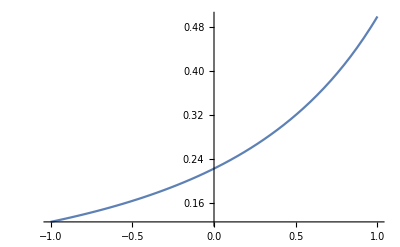

```mathematica
surfj0[s_]=Simplify[Sqrt[Sum[drdxJ[[1]][[k]]*drdxJ[[1]][[k]],{k,1,2}]]]
Plot[surfj0[s],{s,-1,1}]
```

```mathematica
surfj0[1]
```

999/2000

```mathematica
test={{r00,r01},{r10,r11}};
```

```mathematica
test[[1]][[2]]
```

r01

```mathematica
Simplify[drdxJ[[1]][[1]]*drdxJ[[1]][[1]]]
```

(3992004000000 Cos[1/8 π (1+r)]^2)/(2999-999 s)^4

```mathematica
Simplify[drdxJ[[1]][[2]]*drdxJ[[1]][[2]]]
```

(3992004000000 Sin[1/8 π (1+r)]^2)/(2999-999 s)^4

```mathematica
jac1[s_]:=Simplify[xr*(ys)-yr*(xs)];
```

```mathematica
jac1[s]
```

-(499500000 π)/(-2999+999 s)^3

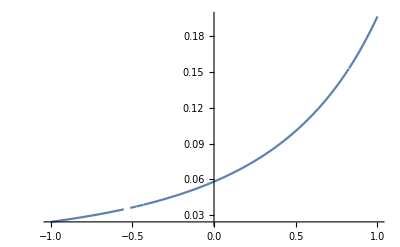

```mathematica
Plot[jac1[s], {s,-1,1}]
```

```mathematica
jac1[1]
```

-(499500000 π)/(-2999+999 s)^3

```mathematica
Integrate[jac1[s]*invr3[s],{s,-1,1},{r,-1,1}]
```